```mathematica
RbData=FileNameJoin[{"Z:","RbData"}];
reports=FileNameJoin[{"C:","Users","karl","Dropbox","00School","gradYear03Fall","research","reports","faradayRotation_11-18"}];
basePath=RbData
```

Z:\RbData

```mathematica
noRot={FileNameJoin[{reports,"noRotation1","FDayScan2016-11-17_"<>"135032"<>"Analysis.dat"}],-0.024285714,0.813714286};
t50b20={FileNameJoin[{reports,"t-50_b-20","FDayScan2016-11-17_"<>"145158"<>"Analysis.dat"}],-0.024285714, 0.570857143};
t60b50={FileNameJoin[{reports,"t-60_b-50","FDayScan2016-11-17_"<>"153940"<>"Analysis.dat"}],-0.024285714, 0.692285714};
t90b10={FileNameJoin[{reports,"t-90_b-10","FDayScan2016-11-19_"<>"195152"<>"Analysis.dat"}],-0.026153846,-0.325846154};
t90b20={FileNameJoin[{reports,"t-90_b-20","FDayScan2016-11-19_"<>"195911"<>"Analysis.dat"}],-0.026153846,-0.979692308};
t90b40={FileNameJoin[{reports,"t-90_b-40","FDayScan2016-11-19_"<>"200636"<>"Analysis.dat"}],-0.026153846,-1.241230769};
t90b60={FileNameJoin[{reports,"t-90_b-60","FDayScan2016-11-19_"<>"202401"<>"Analysis.dat"}],-0.024285714,1.299428571};
t100b10={FileNameJoin[{reports,"t-100_b-10","FDayScan2016-11-19_"<>"214114"<>"Analysis.dat"}],-0.024285714,1.906571429};
t100b20={FileNameJoin[{reports,"t-100_b-20","FDayScan2016-11-19_"<>"212933"<>"Analysis.dat"}],-0.022666667,1.574666667};
t100b40={FileNameJoin[{reports,"t-100_b-40","FDayScan2016-11-19_"<>"212129"<>"Analysis.dat"}],-0.026153846,-1.110461538};
t100b60={FileNameJoin[{reports,"t-100_b-60","FDayScan2016-11-19_"<>"211334"<>"Analysis.dat"}],-0.026153846,-0.456615385};
date1208="2016-12-08";
t150b20={FileNameJoin[{RbData,date1208,"FDayScan"<>date1208<>"_"<>"130736"<>"Analysis.dat"}],-0.0228,10.162}
t140b20={FileNameJoin[{RbData,date1208,"FDayScan"<>date1208<>"_"<>"133837"<>"Analysis.dat"}],-0.024215307, 10.36073742};
t140b20pos={FileNameJoin[{RbData,date1208,"FDayScan"<>date1208<>"_"<>"135650"<>"Analysis.dat"}],-0.023470031 ,19.72082273};
t150b20freq2797={FileNameJoin[{RbData,date1208,"FDayScan"<>date1208<>"_"<>"151000"<>"Analysis.dat"}],-0.021888, 22.480384};
```

{Z:\RbData\2016-12-08\FDayScan2016-12-08_130736Analysis.dat,-0.0228,10.162}

{Z:\RbData\2016-12-08\FDayScan2016-12-08_135650Analysis.dat,-0.02347,19.7208}

21.

20.9

33.849-0.106524 x+0.243996 x^2

95.9324

(19.7208 | -1.12661
18.5473 | -1.10182
17.3738 | -1.10718
16.2003 | -1.09955
15.0268 | -1.08753
13.8533 | -1.09824
12.6798 | -1.07761
11.5063 | -1.07587
10.3328 | -1.07032
9.15931 | -1.04296
7.98581 | -1.02987)

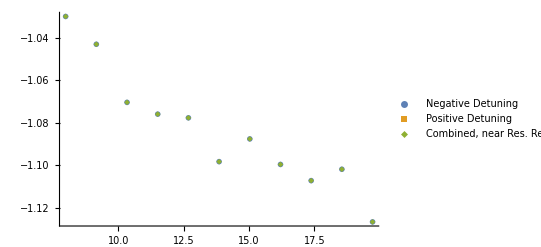

```mathematica
runInfo=t140b20v2
aoutNegConv=runInfo[[2]];
aoutNegInt=runInfo[[3]];
dataNeg=Import[runInfo[[1]],"tsv"];
v1=dataNeg[[11]][[2]]
v2=dataNeg[[12]][[2]]
(*MatrixForm[data]; (*If having difficulty importing, check that file looks like expected*)*)
For[i=1,i<14,i++,(* Deletes Comment lines and header *)
dataNeg=Delete[dataNeg,{{1}}];];
dataNeg=Drop[dataNeg,None,{2,8}]; (* Drops Columns 2 through 8*)
dataNeg=Drop[dataNeg,None,{3,4}]; (* Drops Columns 3 and 4 *)
{aout,θDeg}=Transpose[dataNeg];
{detune,θRad}={aout*aoutNegConv+aoutNegInt,θDeg*Pi/180};
dataNeg=Transpose[{detune,θRad}];
dataNeg2=Transpose[{detune,θRad+1.12405-.000328235*detune}];
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;
c1v2iSlope=.0504;
c1v2iInt=.0113;
c2v2iSlope=.0488;
c2v2iInt=.0069;
i1=v1*c1v2iSlope-c1v2iInt;
i2=v2*c2v2iSlope-c2v2iInt;

getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  
getBEq[i1,i2]
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}]
moredata=0;
If[moredata==1
,
dataPos=Import["/home/karl/Dropbox/00School/gradYear03Fall/research/reports/faradayRotation_11-07/"<>pos60<>"Analysis.dat","tsv"];
aoutPosConv=pos60Conv;
aoutPosInt=pos60Int;
For[i=1,i<14,i++,(* Deletes Comment lines and header *)
dataPos=Delete[dataPos,{{1}}];];
dataPos=Drop[dataPos,None,{2,8}]; (* Drops Columns 2 through 8*)
dataPos=Drop[dataPos,None,{3,4}]; (* Drops Columns 3 and 4 *)
{aout2,θDeg2}=Transpose[dataPos];
{detune2,θRad2}={aout2*aoutPosConv+aoutPosInt,θDeg2*Pi/180};
dataPos=Transpose[{detune2,θRad2}];
alldata=Join[dataNeg,dataPos];
,
alldata=dataNeg;];

MatrixForm[alldata]
ListPlot[{dataNeg,dataPos}];

(* Removes datapoints that wrapped in rotation *)
lowerBoundDetuning=4;
upperBoundDetuning= 30;
dataset=Dataset[alldata];
dataset=dataset[Select[Abs[#[[1]]]<upperBoundDetuning&]];
dataset=dataset[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
alldata = Normal[dataset];
ListPlot[{Legended[dataNeg,"Negative Detuning"],Legended[dataPos,"Positive Detuning"],Legended[alldata,"Combined, near Res. Rem."]},PlotRange->All,PlotMarkers->{Automatic,Large}]
```

a>0

{a→0.025409,b→-0.479967,d→-1.13784}

0.0000533746

{a→0.0170238,d→-1.12734}

0.0000618535

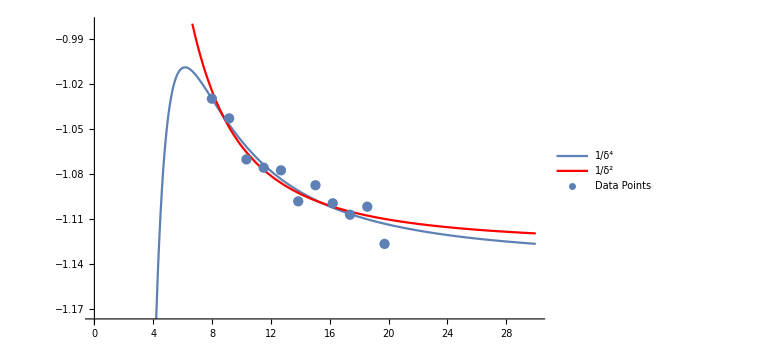

```mathematica
(* Calculates fit for data *)
Clear[a]
$Assumptions=a>0
lowerBoundDetuning=5;
upperBoundDetuning= 30;
dataset=Dataset[alldata];
dataset=dataset[Select[#[[1]]<upperBoundDetuning&]];
dataset=dataset[Select[#[[1]]>lowerBoundDetuning&]];
ListPlot[Normal[dataset]];
νo=377.107;
maxmin={dataset[-1][2],dataset[1][2]};
model=a/(δ)^2(δ+νo)+b/(δ)^4(δ+νo)+d;
replacements =FindFit[Normal[dataset],{model,a>0,a<10},{{a,1},{b,1},{d,0}},δ]
plot=Plot[Legended[Evaluate[model/.replacements],"1/δ^4"],{δ,0,30},PlotRange->{Min[maxmin]-.05,Max[maxmin]+.05}];
modelf=Function[{δ},Evaluate[model/.replacements]];
{δl,θl}=Transpose[Normal[dataset]];
residuals=θl - Map[modelf,δl];
Norm[residuals]^2/(Length[dataset]-1)

modelNo4=a/(δ)^2(δ+νo)+d;
replacementsNo4=FindFit[Normal[dataset],modelNo4,{{a,1},{d,0}},δ]
plotNo4=Plot[Legended[Evaluate[modelNo4/.replacementsNo4],"1/δ^2"],{δ,0,30},PlotRange->{Min[maxmin]-.05,Max[maxmin]+.05},PlotStyle->Red];
modelfNo4=Function[{δ},Evaluate[modelNo4/.replacementsNo4]];
{δl,θl}=Transpose[Normal[dataset]];
residuals=θl - Map[modelfNo4,δl];
Norm[residuals]^2/(Length[dataset]-1)
Show[plot,plotNo4,ListPlot[Legended[alldata,"Data Points"]],ImageSize->Large]
```

```mathematica
c=2.99792458*^10;
re=2.8179*^-13;
fge=0.34231;
k=4/3;
μ=9.2740*^-24;
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}];
h=6.6261*^-34;
ν0=3.77107*^14;
conversionFactor=4*Pi*h*ν0/(BdotL*c*re*fge*k*μ)*(1*^9);
n=(a/.replacements)* conversionFactor
nNo4 =(a/.replacementsNo4)*conversionFactor\
PRb=4*ν0
```

2.32585×10^13

1.5583×10^13